```mathematica
h=6.626070040*10^-34;
NA=6.022140857*10^23;
c=299792458;
k=1.38064852×10^-23;
Translational[m_,ni_List]:=h^2/(8m)Total[#1^2/#2^2&@@@ni];
Rotational[RotationalConstant_,J_]:=RotationalConstant*J*(J+1);
FrequencyToEnergy[quantity_]:=c*100*quantity*h;
```

```mathematica
Translational[10^23*12.01/NA/1000,{{2,0.1},{1,0.1},{1,0.1}}]-Translational[10^23*12.01/NA/1000,{{1,0.1},{1,0.1},{1,0.1}}]
```

8.25565×10^-57

```mathematica
h^2/(10^23*12.01/NA/1000*8*0.1^2)*3
```

8.25565×10^-57

```mathematica
Translational[(12.01+1.008*4)/NA/1000,{{2,0.1},{1,0.1},{1,0.1}}]-Translational[(12.01+1.008*4)/NA/1000,{{1,0.1},{1,0.1},{1,0.1}}]
```

6.18067×10^-40

```mathematica
4*5.24120
```

20.9648

```mathematica
FrequencyToEnergy[20.9648]
```

4.16454×10^-20

```mathematica
FrequencyToEnergy[3019]
```

5.99708×10^-18

```mathematica
FrequencyToEnergy[1306]
```

2.5943×10^-18

```mathematica
{%98,%99,%100}/%102//TableForm//TeXForm
```

\begin{array}{c}
 6.73801\times 10^9 \\
 9.70296\times 10^{11} \\
 4.19744\times 10^{11} \\
\end{array}

```mathematica
Translational[(12.01+1.008*4)/NA/1000,{{2,#},{1,#},{1,#}}]-Translational[(12.01+1.008*4)/NA/1000,{{1,#},{1,#},{1,#}}]&/@{100*10^-9,1}//TraditionalForm
```

{6.18067×10^-22,6.18067×10^-36}

```mathematica
FrequencyToEnergy[#]&/@(4*{2.51967,0.68341})//TeXForm
```

\{\text{2.002075179916342$\grave{ }$*${}^{\wedge}$-20},\text{5.4302277627888856$\grave{
   }$*${}^{\wedge}$-21}\}

```mathematica
FrequencyToEnergy[#]&/@(4*{2.51967,0.68341})
```

{2.00208×10^-20,5.43023×10^-21}

```mathematica
TeXForm/@%115
```

{\text{2.002075179916342$\grave{ }$*${}^{\wedge}$-20},\text{5.4302277627888856$\grave{ }$*${}^{\wedge}$-21}}

```mathematica
Translational[28.01/NA/1000,{{2,0.1},{1,0.1},{1,0.1}}]-Translational[28.01/NA/1000,{{1,0.1},{1,0.1},{1,0.1}}]
```

3.53982×10^-34

```mathematica
FrequencyToEnergy[1.93128*4]
```

1.53455×10^-20

```mathematica
1076.4*1000/NA
```

1.7874×10^-18

```mathematica
30!//N
```

2.65253×10^32

----------------------------------------------------------

```mathematica
MetaModel[left_,total_]:=(total!/left!/(total-left)!)^2;
StirlingApproximation[n_]:=Sqrt[2Pi n](n/E)^n;
LogStirlingApproximation[n_]:=n Log[n]-n+0.5Log[2Pi n];
GrandMetaModel[left_,total_]:=(StirlingApproximation[total]/StirlingApproximation[left]/StirlingApproximation[total-left])^2;
GrandMetaModelEntropy[left_,total_]:=2k(LogStirlingApproximation[total]-LogStirlingApproximation[left]-LogStirlingApproximation[total-left]);
```

```mathematica
Table[{i,MetaModel[i,10],MetaModel[i,10]/Sum[MetaModel[q,10],{q,10}]//N},{i,0,10}]//TableForm//TeXForm
```

\begin{array}{ccc}
 0 & 1 & \text{5.4125734080268465$\grave{ }$*${}^{\wedge}$-6} \\
 1 & 100 & 0.000541257 \\
 2 & 2025 & 0.0109605 \\
 3 & 14400 & 0.0779411 \\
 4 & 44100 & 0.238694 \\
 5 & 63504 & 0.34372 \\
 6 & 44100 & 0.238694 \\
 7 & 14400 & 0.0779411 \\
 8 & 2025 & 0.0109605 \\
 9 & 100 & 0.000541257 \\
 10 & 1 & \text{5.4125734080268465$\grave{ }$*${}^{\wedge}$-6} \\
\end{array}

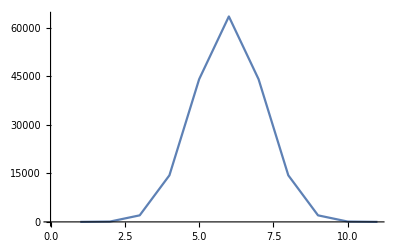

```mathematica
Table[MetaModel[i,10],{i,0,10}]//ListLinePlot
```

```mathematica
Table[GrandMetaModel[i,500000],{i,0.45*500000,0.55*500000}]//ListLinePlot
```

$Aborted

```mathematica
Transpose[{i,GrandMetaModel[500000*i,500000]/GrandMetaModel[0.5*500000,500000]}/.i->{0.45,0.49,0.499,0.4999,0.5001,0.501,0.51,0.55}]//TableForm//TeXForm
```

\begin{array}{cc}
 0.45 & \text{7.91188716355642522152$\grave{ }$8.794267295286247*${}^{\wedge}$-2176} \\
 0.49 & \text{1.366110571127922112894500169$\grave{ }$8.827777965412546*${}^{\wedge}$-87}
   \\
 0.499 & 0.135335644 \\
 0.4999 & 0.98019871 \\
 0.5001 & 0.98019871 \\
 0.501 & 0.135335644 \\
 0.51 & \text{1.3661105704122592048574738954$\grave{
   }$8.845558340937217*${}^{\wedge}$-87} \\
 0.55 & \text{7.91188715941163321556$\grave{ }$8.883458299397237*${}^{\wedge}$-2176} \\
\end{array}

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/物理化学作业/figures"]
```

/Users/Apple/Documents/GitHub/LaTeX-Files/物理化学作业/figures

```mathematica
Export["distributionsimplified.eps",Transpose[{i,GrandMetaModel[500000*i,500000]/GrandMetaModel[0.5*500000,500000]}/.i->{0.45,0.49,0.499,0.4999,0.5001,0.501,0.51,0.55}]//ListLinePlot]
```

distributionsimplified.eps

```mathematica
Export["distributionenhanced.eps",ListLinePlot[Transpose[{i,GrandMetaModel[500000*i,500000]/GrandMetaModel[0.5*500000,500000]}/.i->Table[q,{q,0.45,0.55,0.0001}]],PlotRange->All]]
```

distributionenhanced.eps

```mathematica
FindRoot[GrandMetaModel[x*500000,500000]/GrandMetaModel[0.5*500000,500000]==0.5,{x,0.4995}]
2*(0.5-x/.%)
```

{x→0.499411}

0.00117741

```mathematica
FindRoot[MetaModel[x*500,500]/GrandMetaModel[0.5*500,500]==0.5,{x,0.4995}]
2*(0.5-x/.%)
```

{x→0.48138}

0.037239

```mathematica
NumberForm[GrandMetaModelEntropy[0.125NA+500000,0.25NA],16]
```

2.881572205420942

```mathematica
NumberForm[GrandMetaModelEntropy[0.125NA,0.25NA],16]
```

2.881572205420942

```mathematica
NumberForm[GrandMetaModelEntropy[0.125NA+500000000,0.25NA],16]
```

2.881572205420942

```mathematica
5.763144410841943
```

```mathematica
5.763144410841885
```

```mathematica
FindRoot[GrandMetaModelEntropy[x+0.125NA,0.25NA]==GrandMetaModelEntropy[0.125NA,0.25NA]-0.0001,{x,0.001NA}]
```

{x→5.22122×10^20}

```mathematica
N[(0.125NA+5.221221965397577*^20)/0.125/NA,4]
```

1.00694

```mathematica
NSolve[h/8/Pi^2/i/(c*100)==0.1142,i]
```

{{i→2.4512×10^-45}}

```mathematica
(127*35)/(127+35)/1000/NA
```

4.55623×10^-26

```mathematica
Solve[4.5562321201844107*^-26*x^2==2.4512*10^-45,x]
```

{{x→-2.31946×10^-10},{x→2.31946×10^-10}}

```mathematica
h/8/Pi^2/((12*16)/(12+16)/1000/NA*(112.81*10^-12)^2)/(c*100)
```

1.93178

```mathematica
4*1.93178
```

7.72712

```mathematica
2991*(c*100)//N
```

8.96679×10^13

```mathematica
Solve[Sqrt[x/((1*35)/(1+35)/1000/NA)]==8.96679241878*^13,x]
```

{{x→12.9804}}

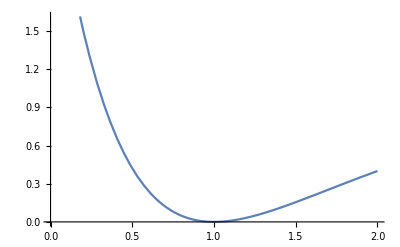

```mathematica
Plot[(1-Exp[-(x-1)])^2,{x,0,2}]
```

```mathematica
x(x+1)-
```

```mathematica
h*c*4138*100/4/(556.2*1000)*NA
```

0.0222499

```mathematica
%*4138
```

92.0699

```mathematica
Solve[0.02224985294716193*(x+0.5)==0.25,x]
```

{{x→10.736}}

```mathematica
h/8/Pi^2/((14*14)/(14+14)*(109.8*10^-12)^2/1000/NA)/(c*100)
```

1.99753

```mathematica
14*1.99753
```

27.9654

```mathematica
20623-27.9654
```

20595.

```mathematica
Solve[Table[(x+0.5)*y-(x+0.5)^2*a*y,{x,1,3}]-((x+0.5)*y-(x+0.5)^2*z*a*y/.x->0)=={2345.15,4661.4,6983.73},{y,a,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→2304.09,a→-0.00131939,z→-45.0263}}

```mathematica
Table[(x+0.5)*y-(x+0.5)^2*a*y,{x,1,3}]-((x+0.5)*y-(x+0.5)^2*a*y/.x->0)
```

{1. y-2. a y,2. y-6. a y,3. y-12. a y}

```mathematica
NonlinearModelFit[{{1,2345.15},{2,4661.4},{3,6983.73}},(x+0.5)*y-(x+0.5)^2*a*y-0.5y-0.25a y,{a,y},x]
```

FittedModel[-1179.65+2355.88 (0.5+x)-6.85252 (0.5+x)^2]

```mathematica
--------------------------------------------------------------
```

```mathematica
BoltzmannDistribution[EnergyList_,T_]:=#/Total[#]&@Exp[-EnergyList/k/T];
BoltzmannDistributionPartitionFunction[EnergyList_,T_]:=Total[Exp[-EnergyList/k/T]];
TranslationalPartitionFunction[m_,V_,T_]:=(2 Pi m )^(3/2)/h^3(k T)^(3/2)V;
JTomeV[J_]:=J/(1.6*10^-19)*1000;
```

```mathematica
b=100;
BoltzmannDistributionFunction[Translational[31.9988/NA,{{#1,0.1},{#2,0.1},{#3,0.1}}]&@@@Flatten[Table[{a1,a2,a3},{a1,b},{a2,b},{a3,b}],2],300]
Clear[b]
```

1.×10^6

```mathematica
TranslationalPartitionFunction[31.9988/NA/1000,0.001,300]
```

1.76759×10^29

```mathematica
Exp[-Translational[31.9988/NA/1000,{{1,0.1},{1,0.1},{1,0.1}}]/k/300]/TranslationalPartitionFunction[31.9988/NA/1000,0.001,300]*0.001NA
```

3.40697×10^-9

```mathematica
3*Exp[-Translational[31.9988/NA/1000,{{2,0.1},{1,0.1},{1,0.1}}]/k/300]/TranslationalPartitionFunction[31.9988/NA/1000,0.001,300]*0.001NA
```

1.02209×10^-8

```mathematica
JTomeV[FrequencyToEnergy[1580.161]]
```

19.6182

```mathematica
JTomeV[FrequencyToEnergy[1.450*2]]
```

0.0360043

```mathematica
Exp[-%/25]
```

0.998561

```mathematica
JTomeV[Translational[31.9988/NA/1000,{{2,0.1},{1,0.1},{1,0.1}}]-Translational[31.9988/NA/1000,{{1,0.1},{1,0.1},{1,0.1}}]]
```

1.9366×10^-18

```mathematica
Exp[-#/25]&/@{%47,%46,%45}
```

{1.,0.99928,0.456245}

```mathematica
6-311+G(3df,2p) CCSD(T)=FULL  -> 1.450
```

```mathematica
Solve[Exp[-x/k/300]==0.3/0.7,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.50946×10^-21}}

```mathematica
3.5094616108282785*^-21*NA/1000
```

2.11345

```mathematica
1/(Exp[-3.5094616108282785*^-21/k/400]+1)
```

0.653729

```mathematica
1-%80
```

0.346271

```mathematica
1/(Exp[-3.5094616108282785*^-21/k/200]+1)
```

0.780905

```mathematica
1-%
```

0.219095

```mathematica
Solve[Exp[-(19.3*10^3-0.87*10^3)/6*Pi*(10^-8)^3*g*0.01/k/300]==1/1000,g]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{g→296.495}}

```mathematica
1000000/NA/57.595
```

2.88313×10^-20

```mathematica
pm=43;
pm*Exp[-(1*10^3-1.29)*1/6*Pi*(2.5*10^-6)^3*9.8*300/k/300]
```

7.2243329481746839`6.191188779409614*^-2518751383

```mathematica
1000000/NA/57.573
```

2.88423×10^-20

```mathematica
25*1.6*10^-22/k
```

289.719

```mathematica
------------------------ex----------------------------------------
```

```mathematica
(TranslationalPartitionFunction[18/NA,0.001,300])^(1/3)
```

1.33106×10^11

```mathematica
VibrationalPartitionFunction[neu_,T_]:=1/(1-Exp[-h*c*neu*100/k/T]) ;
(*neu请用cm^-1 单位*)
LinearRotationalPartitionFunction[B_,T_]:=1/h/c/(B*100)*k*T;
(*B请用cm^-1 单位*)
```

```mathematica
Exp[-#*h*1595*c*100/k/300]&/@{0,1,2}
```

{1.,0.000476282,2.26845×10^-7}

```mathematica
Limit[Sum[Exp[-a],{a,0,q}]//Simplify,q->Infinity]
```

ⅇ/(-1+ⅇ)

```mathematica
h*FrequencyToEnergy[1595]
```

2.09939×10^-53

```mathematica
VibrationalPartitionFunction[1595,300]
```

1.00048

```mathematica
VibrationalPartitionFunction[2143,300]
```

1.00003

```mathematica
VibrationalPartitionFunction[192,300]
```

1.66166

```mathematica
TranslationalPartitionFunction[28/NA,0.001,300]
```

4.57529×10^33

```mathematica
VibrationalPartitionFunction[1595,300]
```

1.00048

```mathematica
--------------------------------------------------------------------
```

```mathematica
TranslationalPartitionFunction[m_,V_,T_]:=(2 Pi m )^(3/2)/h^3(k T)^(3/2)V;
(*国际单位制*)
VibrationalPartitionFunction[neu_,T_]:=1/(1-Exp[-h*c*neu*100/k/T]) ;
(*neu请用cm^-1 单位*)
LinearRotationalPartitionFunction[B_,T_]:=1/h/c/(B*100)*k*T;
(*B请用cm^-1 单位*)
RotationalPartitionFunction[B_List,T_]:=(k T/h/c)^(3/2) (Pi/(Times@@B)/100^3)^(1/2);
```

```mathematica
TranslationalPartitionFunction[m_,V_,T_]:=(2 Pi m )^(3/2)/h^3(k T)^(3/2)V;
PartitionFunctionToEnergy[N_,PartitionFunction_,variable_]:=N*k*variable^2*D[Log[PartitionFunction],variable];
GasTotalPartitionFunction[m_,V_,neu_List,B_List,T_]:=TranslationalPartitionFunction[m,V,T]*(Times@@(VibrationalPartitionFunction[#,T]&/@neu))*RotationalPartitionFunction[B,T];
LinearGasTotalPartitionFunction[m_,V_,neu_List,B_,T_]:=TranslationalPartitionFunction[m,V,T]*(Times@@(VibrationalPartitionFunction[#,T]&/@neu))*LinearRotationalPartitionFunction[B,T];
PartitionFunctionToHelmholtz[N_,PartitionFunction_,variable_]:=-N*k*variable*Log[PartitionFunction];
DelocalizedPartitionFunctionToHelmholtz[N_,PartitionFunction_,variable_]:=-N*k*variable*Log[PartitionFunction]+k*variable*LogStirlingApproximation[N];
PartitionFunctionToEntropy[N_,PartitionFunction_,variable_]:=-D[PartitionFunctionToHelmholtz[N,PartitionFunction,variable],variable];
DelocalizedPartitionFunctionToEntropy[N_,PartitionFunction_,variable_]:=-D[DelocalizedPartitionFunctionToHelmholtz[N,PartitionFunction,variable],variable];
```

```mathematica
DelocalizedPartitionFunctionToEntropy[NA,LinearGasTotalPartitionFunction[32/1000/NA,NA*k*T/1.01325/10^5,{1580.161},1.450,T],T]/.T->298
```

209.877

```mathematica
DelocalizedPartitionFunctionToEntropy[NA,LinearGasTotalPartitionFunction[32/1000/NA,NA*k*T/1.01325/10^5,{1580.161},1.478,T],T]/.T->298
```

DelocalizedPartitionFunctionToEntropy[6.02214×10^23,5.99988×10^32,298]

```mathematica
DelocalizedPartitionFunctionToEntropy[NA,LinearGasTotalPartitionFunction[2.016/1000/NA,NA*k*T/1.01325/10^5,{4401.213},60.748,T],T]/.T->298
```

144.307

```mathematica
PartitionFunctionToEnergy[NA,Total[#/#[[1]]]&@BoltzmannDistribution[{0,3.50946*10^-21},T],T]/.T->300
```

```mathematica
634.0340461660198
```

```mathematica
PartitionFunctionToEntropy[NA,Total[#/#[[1]]]&@BoltzmannDistribution[{0,3.50946*10^-21},T],T]/.T->300
```

5.07901

```mathematica
{#1,#2,#3,#2/#3}&@@@({#,PartitionFunctionToEnergy[NA,VibrationalPartitionFunction[#,T],T],PartitionFunctionToEnthalpy[NA,VibrationalPartitionFunction[#,T],T]}&@Sort[{2954,1388,995,289,2896,1379,2969,1468,1190,2985,1469,822}]/.T->300//Transpose)
```

{{289,1152.82,6.23541,184.883},{822,194.586,0.811545,239.773},{995,101.604,0.409354,248.207},{1190,47.45,0.185834,255.335},{1379,22.1684,0.0850602,260.62},{1388,21.3692,0.0819244,260.841},{1468,15.3929,0.0585943,262.703},{1469,15.3296,0.0583485,262.725},{2896,0.0321893,0.000115023,279.851},{2954,0.024861,0.0000887194,280.22},{2969,0.0232528,0.0000829528,280.314},{2985,0.0216513,0.0000772124,280.412}}

```mathematica
{#1,#2,#3,#2/#3}&@@@({#,PartitionFunctionToEnergy[NA,VibrationalPartitionFunction[#,T],T],PartitionFunctionToEntropy[NA,VibrationalPartitionFunction[#,T],T]}&@Sort[{2954,1388,995,289,2896,1379,2969,1468,1190,2985,1469,822}]/.T->300//Transpose)//TableForm//TeXForm
```

\begin{array}{cccc}
 289 & 1152.82 & 6.23541 & 184.883 \\
 822 & 194.586 & 0.811545 & 239.773 \\
 995 & 101.604 & 0.409354 & 248.207 \\
 1190 & 47.45 & 0.185834 & 255.335 \\
 1379 & 22.1684 & 0.0850602 & 260.62 \\
 1388 & 21.3692 & 0.0819244 & 260.841 \\
 1468 & 15.3929 & 0.0585943 & 262.703 \\
 1469 & 15.3296 & 0.0583485 & 262.725 \\
 2896 & 0.0321893 & 0.000115023 & 279.851 \\
 2954 & 0.024861 & 0.0000887194 & 280.22 \\
 2969 & 0.0232528 & 0.0000829528 & 280.314 \\
 2985 & 0.0216513 & 0.0000772124 & 280.412 \\
\end{array}

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/物理化学作业/figures"]
```

/Users/Apple/Documents/GitHub/LaTeX-Files/物理化学作业/figures

```mathematica
Export["Energy.eps",Plot[PartitionFunctionToEnergy[NA,VibrationalPartitionFunction[x,T],T]/.T->300,{x,100,4000},Axes->False,Frame->True,FrameLabel->{"Wavelength/cm^-1","Energy/(J/mol)"}]]
```

Energy.eps

```mathematica
Export["Entropy.eps",Plot[PartitionFunctionToEnthalpy[NA,VibrationalPartitionFunction[x,T],T]/.T->300,{x,100,4000},Axes->False,Frame->True,FrameLabel->{"Wavelength/cm^-1","Entropy/(J/K/mol)"}]]
```

Entropy.eps

```mathematica
DelocalizedPartitionFunctionToEntropy[NA,TranslationalPartitionFunction[32/1000/NA,1,T],T]/.T->0.00000000000000000000000000001
```

-721.035

```mathematica
%/.T->300
```

-298.506

```mathematica
PartitionFunctionToEntropy[NA,1,T]/.T->300
```

0